```mathematica
Integrate[(Sin[n*Pi*x/a])^2,{x,0,a}]
```

1/4 a (2-Sin[2 n π]/(n π))

```mathematica
psi[x_,a_,n_]:=Sqrt[2/a]*(Sin[n*Pi*x/a])
```

```mathematica
psi[x,a,n]
```

√2 √(1/a) Sin[(n π x)/a]

```mathematica
Integrate[psi[x,a,1]*x*psi[x,a,1],{x,0,a}]
```

a/2

```mathematica
Integrate[psi[x,a,5]*x*psi[x,a,5],{x,0,a}]
```

a/2

```mathematica
Integrate[psi[x,a,n]*x*psi[x,a,n],{x,0,a}]
```

-(a (-1-2 n^2 π^2+Cos[2 n π]+2 n π Sin[2 n π]))/(4 n^2 π^2)

```mathematica
Integrate[psi[x,a,1]*-I*hbar*D[psi[x,a,1],x],{x,0,a}]
```

0

```mathematica
Integrate[psi[x,a,n]*-I*hbar*D[psi[x,a,n],x],{x,0,a}]
```

-(ⅈ hbar Sin[n π]^2)/a

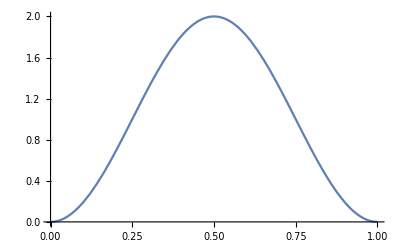

```mathematica
Plot[psi[x,1,1]*psi[x,1,1],{x,0,1}]
```

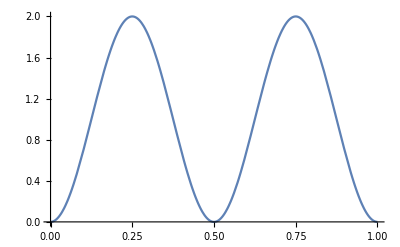

```mathematica
Plot[psi[x,1,2]*psi[x,1,2],{x,0,1}]
```

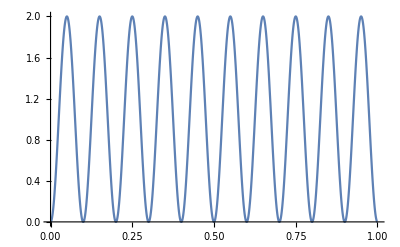

```mathematica
Plot[psi[x,1,10]*psi[x,1,10],{x,0,1}]
```

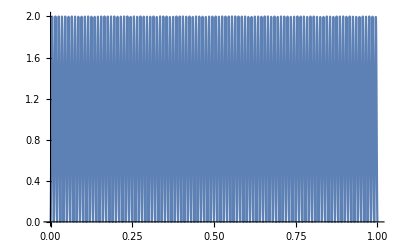

```mathematica
Plot[psi[x,1,100]*psi[x,1,100],{x,0,1}]
```